# Electrons interacting with a 1D periodic potential.

Greis J. Kim Reyes

Department of Physics and Astronomy
SUNY New Paltz

Simple problems of electrons interacting with a 1D periodic potential:

Define Physical & Numerical Constants

✅ Steps to Solve the 1D Electron Model interacting with a periodic potential

1. Define Physical & Numerical Constants  
   - Set ℏ = 1, m = 1, lattice constant a, potential strength V₀, etc.  
   - Choose a range of crystal momenta k values (to sweep through the Brillouin zone)

2. Choose Number of Plane Waves  
   - Decide how many basis functions to include (e.g., 5 plane waves)  
   - Define the wavevectors: k + nG, where G = 2π/a and n = -N, ..., N

3. Write the Potential in Fourier Space  
   - Express V(x) = V₀ cos(2πx/a) = (V₀/2)(e^{iGx} + e^{-iGx})  
   - So the only nonzero Fourier components are: V_G = V_{−G} = V₀/2

4. Construct the Hamiltonian Matrix  
   - Diagonal elements: kinetic energy → H_{G,G} = (ℏ.b2 / 2m)(k + G).b2  
   - Off-diagonal elements: potential couplings → H_{G,G’} = V_{G’ − G}, only nonzero if G’ − G = ±G

5. Solve the Eigenvalue Problem  
   - For each k, solve H(k) C = E C  
   - Store eigenvalues E(k) — these are your energy bands

6. Plot the Band Structure  
   - Plot Eₙ(k) versus k over the first Brillouin zone to visualize bands and gaps

```mathematica
Quit
```

```mathematica
(*Constants and lattice spacing*)
hbar=1;m=1;a=1;  (*atomic units*)
V0=6;  (*strength of the periodic potential, you can change this value and see how the band gap opens*)
```

The plane wave basis is infinite, since there are infinitely many reciprocal lattice vectors, We truncate the basis to a finite number of plane waves

In this example we will use 5 plane waves

The Hamiltonian is a 5x5 matrix

We will include -2G0, -G0, 0, G0, 2G0

The tradeoff:

	*	More plane waves = more accuracy (especially at higher energies)

	*	But larger matrices = more computation time

Let’s define our G vectors.

Recall, Our basis is determine by Bloch’s theorem




The wavefunction is expanded in the  basis.

```mathematica
G0=2*Pi/a;
Glist=G0*Range[-2,2];  (*list of reciprocal lattice vectors, we are expanding our wave function with 5 plane waves*)
```

And choose a potential:

Since , 

its Fourier series is:



So the coefficients .

```mathematica
VG[G_]:=Which[
G==G0||G==-G0,V0/2,(*if G is+G0 or-G0,return V0/2*)
True,0              (*otherwise,return 0*)
];
```

The Hamiltonian matrix elements are:



Recall:



Which gives 1 if G’=G and zero if G’ different to G (you’re integrating a pure oscillating function over a full period — the result is zero due to orthogonality.)

Now since:







This integral is nonzero only when the exponent vanishes, i.e.,



(In our problem )
So we find:



The potential matrix elements connect different plane waves (with different 𝐺) only if G-G’ matches a reciprocal lattice vector and as long as  

Explicitly for this problem 


 ... and same situation will happen to all diagonal elements



and so on...

|                    | $k - 2G$ | $k - G$ | $k$ | $k + G$ | $k + 2G$ |
| --------      | ----------- | -------    | --- | ------- | -------- |
| $k - 2G$  | 🟩           | ✅         | ❌   | ❌       | ❌        |
| $k - G$    | ✅           | 🟩          | ✅   | ❌       | ❌        |
| $k$           | ❌           | ✅          | 🟩  | ✅       | ❌        |
| $k + G$    | ❌          | ❌          | ✅   | 🟩      | ✅        |
| $k + 2G$ | ❌          | ❌           | ❌   | ✅       | 🟩       |

```mathematica
H[kval_]:=Table[KroneckerDelta[G1,G2]*hbar^2*(kval+G1)^2/(2*m)+VG[G1-G2],{G1,Glist},{G2,Glist}]
```

```mathematica
H[kval]//MatrixForm
```

(1/2 (kval-4 π)^2 | 3/2 | 0 | 0 | 0
3/2 | 1/2 (kval-2 π)^2 | 3/2 | 0 | 0
0 | 3/2 | kval^2/2 | 3/2 | 0
0 | 0 | 3/2 | 1/2 (kval+2 π)^2 | 3/2
0 | 0 | 0 | 3/2 | 1/2 (kval+4 π)^2)

Evaluate the Hamiltonian for different values of  𝑘 and extract energy eigenvalues.

```mathematica
kVals=Range[-Pi/a,Pi/a,0.05];  (*Generate a list of values of the crystal momentum. 
 0.05 is the step size (you can make it smaller for smoother bands)*)
bands=Table[
Sort[Eigenvalues[H[k]]],{k,kVals}
]; (*Solves the eigenvalue problem and sort ensures the eigenvalues are in ascending order so the band 1, for example is the lowest... The command Table[loops over all k values in the brillouin zone]*)
```

The output looks like 
bands = {
  {E₁(k₁), E₂(k₁), E₃(k₁), ...},
  {E₁(k₂), E₂(k₂), E₃(k₂), ...},
  ...
}

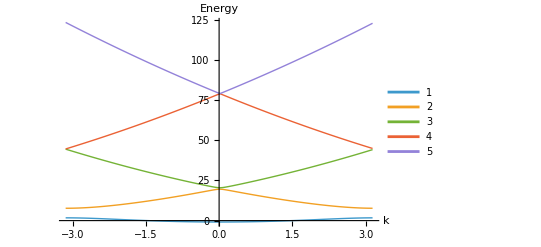

```mathematica
ListLinePlot[Transpose[bands],DataRange->{-Pi/a,Pi/a},PlotRange->All,AxesLabel->{"k","Energy"},PlotLegends->Automatic,PlotStyle->Thick]
```